```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/675nm.dat"]
```

{{1.83648,0.102737},{1.67469,0.155036},{1.55096,0.153408},{1.77833,0.139936},{1.08395,0.247329},{1.0884,1.62062},{1.10777,0.189794},{1.1184,0.208558},{1.90886,0.0889262}}

1.27683-0.652966 x

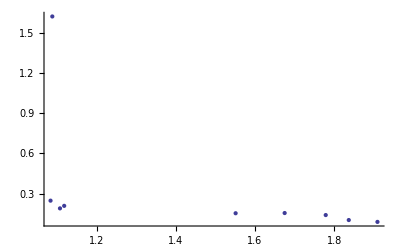

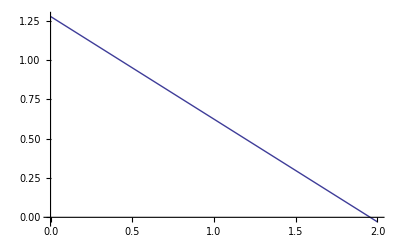

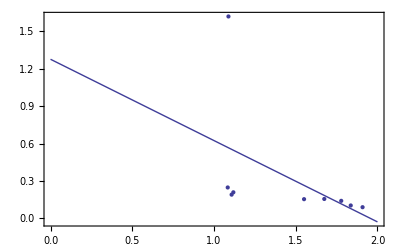

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```